```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

### Highway Problems

#### Ex. 0: Effect of structural condition

```mathematica
defVel[F1,{{0,-1},{0,1},{-1,0},{1,0}}]
LabeledPolarHullPlot[F1]
```

-Graphics-

```mathematica
pwThorughPoints[pts_List]:=Function[{x},Evaluate[With[{srPairs=Most@rotatedPairs@SortBy[#,First]&@pts},
Piecewise[((({{lineThroughPointsY[#1,#2],x≤#2⟦1⟧}}&)@@First[#])~Join~(({lineThroughPointsY[#1,#2],#1⟦1⟧<x≤#2⟦1⟧}&)@@@Most@Rest@#)~Join~(({{lineThroughPointsY[#1,#2],#1⟦1⟧≤x}}&@@Last@#)))&[srPairs]]
]]]
```

{-1,1/2}

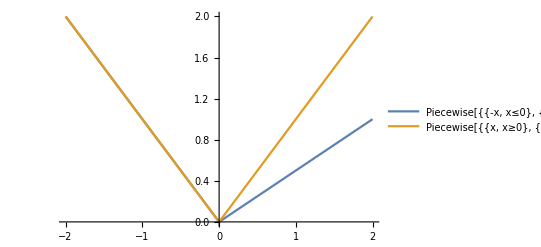

```mathematica
(* define g as line passing through points *)
linePoints={{0,0},{-1,1},2*{1,1/2}};
dualList=({u,v}↦(v⟦2⟧-u⟦2⟧)/(v⟦1⟧-u⟦1⟧))@@@Most@rotatedPairs@SortBy[#,First]&@linePoints
g=pwThorughPoints[linePoints];

{nslope,pslope}=hullMagFunc[Subscript[F1, pt]]/@{-π,0};
g2[t_]:=Piecewise[{{1/pslope*t, t≥0}, {-1/nslope*t, t<0}}]

Plot[{g[x],g2[x]},{x,-2,2},PlotLegends->{{g[x],g2[x]},{"Boundary γ","Velocity γ"}}]
```

```mathematica
DDisk[reg_,c_,r_]:=TransformedRegion[reg,TranslationTransform[c]@*ScalingTransform[{r,r}]]
```

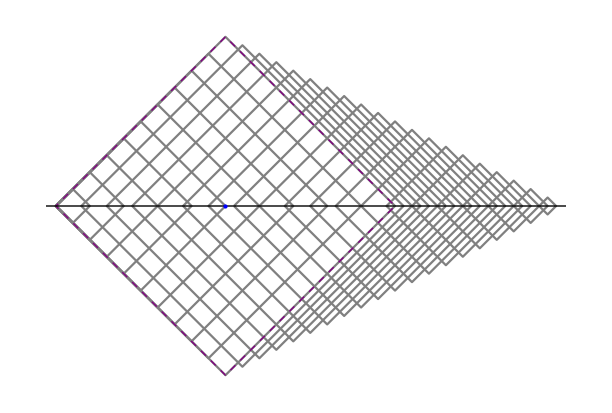

```mathematica
remainingTime[T_,t_]:=Max[0,T-g[t]]/.x->t
conePts=(First/@(SortBy[#,First]&@linePoints)⟦2;;-2⟧);

T=2.5;
a={0,0};p={1,0};l[t_]:=a+t p;n=r90.p;lInv[v_]:=First@v

Show[{
RegionPlot[#,BoundaryStyle->Gray,PlotStyle->None,Frame->False,PerformanceGoal->"Speed"]&/@Table[DDisk[Subscript[F1, reg],l[t],remainingTime[T,t]],{t,-5,5,.25}],
RegionPlot[#,BoundaryStyle->Directive[Purple,Thick,Dashed],PlotStyle->None,Frame->False,PerformanceGoal->"Speed"]&/@Table[DDisk[Subscript[F1, reg],{v,0},remainingTime[T,v]],{v,conePts}],
Graphics[{
Thick,Black,InfiniteLine[{l[0],l[1]}],
PointSize[Large],Blue,Point[{#,0}]&/@conePts
}]
},(*Epilog->{
Inset[PolarHullPlot[F1,ImageSize->Small],{Right,Bottom},{Right,Bottom}]
},*)PlotRange->All,AspectRatio->{1,1},ImageSize->{600,Automatic}]
```

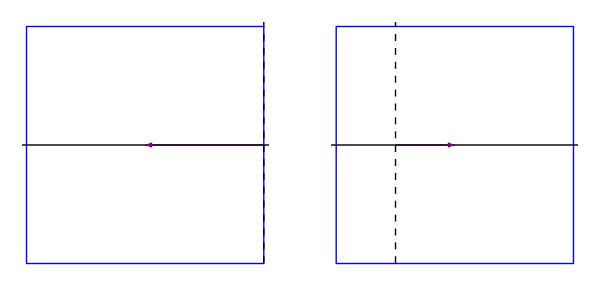

```mathematica
GraphicsRow[Show[{
RegionPlot[
TransformedRegion[(F1^°)_reg,TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
PlotStyle->Transparent,BoundaryStyle->Directive[{Thick,Blue}],Frame->False],
Graphics[{
Thick,Purple,Arrow[{{0,0},#}],
Black,InfiniteLine[{0,0},{1,0}],Dashed,InfiniteLine[{0,0},{0,1}]
}]
},Axes->False,PlotRange->All,AspectRatio->{1,1}]&[{#,0}]&/@duals,
ImageSize->{600,Automatic}]
```

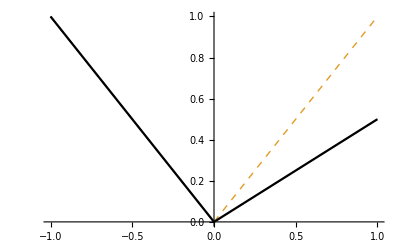

```mathematica
Show[{
Plot[{g[x],g2[x]},{x,-1,1},PlotStyle->Directive[Dashed,Thick]],
Plot[Min[g[x],g2[x]],{x,-1,1},PlotStyle->Black]
}]
```

```mathematica
defVel[F1new,{{0,-1},{0,1},{-1,0},{2,0}}]
LabeledPolarHullPlot[F1new]
```

-Graphics-

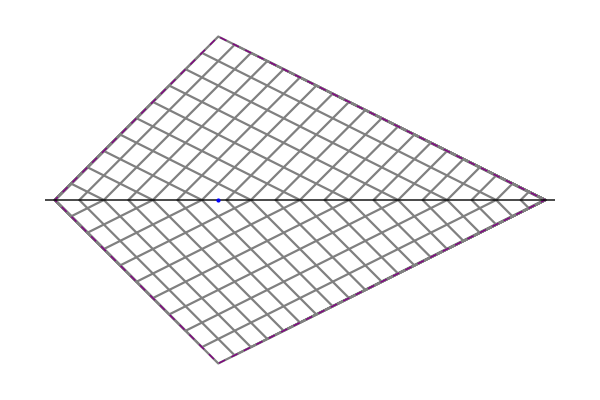

```mathematica
remainingTime[T_,t_]:=Max[0,T-g[t]]/.x->t
conePts=(First/@(SortBy[#,First]&@linePoints)⟦2;;-2⟧);

T=2.5;
a={0,0};p={1,0};l[t_]:=a+t p;n=r90.p;lInv[v_]:=First@v

Show[{
RegionPlot[#,BoundaryStyle->Gray,PlotStyle->None,Frame->False,PerformanceGoal->"Speed"]&/@Table[DDisk[Subscript[F1new, reg],l[t],remainingTime[T,t]],{t,-5,5,.25}],
RegionPlot[#,BoundaryStyle->Directive[Purple,Thick,Dashed],PlotStyle->None,Frame->False,PerformanceGoal->"Speed"]&/@Table[DDisk[Subscript[F1new, reg],{v,0},remainingTime[T,v]],{v,conePts}],
Graphics[{
Thick,Black,InfiniteLine[{l[0],l[1]}],
PointSize[Large],Blue,Point[{#,0}]&/@conePts
}]
},(*Epilog->{
Inset[PolarHullPlot[F1,ImageSize->Small],{Right,Bottom},{Right,Bottom}]
},*)PlotRange->All,AspectRatio->{1,1},ImageSize->{600,Automatic}]
```

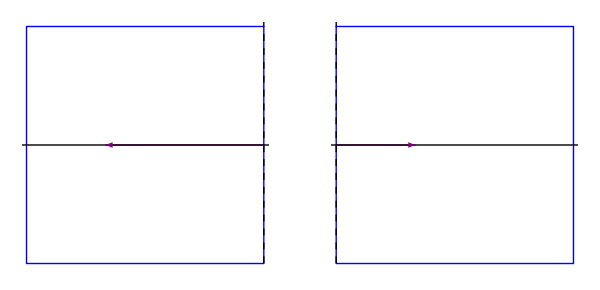

```mathematica
GraphicsRow[Show[{
RegionPlot[
TransformedRegion[(F1new^°)_reg,TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
PlotStyle->Transparent,BoundaryStyle->Directive[{Thick,Blue}],Frame->False],
Graphics[{
Black,InfiniteLine[{0,0},{1,0}],
Thick,Purple,Arrow[{{0,0},#}],
Black,Dashed,InfiniteLine[{0,0},{0,1}]
}]
},Axes->False,PlotRange->All,AspectRatio->{1,1}]&[{#,0}]&/@duals,
ImageSize->{600,Automatic}]
```

```mathematica
LF Conjugates
Easy:By Definition Using MaxValue
LFConj[f_]:=Module[{x,X},X=Array[Subscript[x,##]&,{Length@{##}}];
MaxValue[{##}.X-f[Sequence@@X],X]]&
In[73]:=LFConj[Abs][p]
LFConj[Ramp][p]
Out[73]={∞ p>1||p<-1
0 True


Out[74]={∞ p>1||p<0
0 True


In[133]:=LFConj[a #+b&][p]
LFConj[#1^2+#2^2&][p1,p2]
Out[133]={-b a==p
∞ True


Out[134]=1/4 (p1^2+p2^2)
In[132]:=LFConj[#1+#2+#3&][p1,p2,p3]
Out[132]={∞ (p3==1&&p2>1)||(p3==1&&p2<1)||(p3==1&&p2==1&&p1>1)||(p3==1&&p2==1&&p1<1)||p3>1||p3<1
0 True


Known Values
LFConj[Subscript[ℐ,R_]]:=Subscript[σ,R]
Moreau Envelopes
In[115]:=Subscript[e,λ_][f_]:=x/.Solve[MinValue[f[y]+Abs[y-x]/(2λ),y],x]
Subscript[e,λ][#^2&]
During evaluation of In[115]:=Solve::naqs:MinValue[y^2+Abs[-x+y]/(2 λ),y] is not a quantified system of equations and inequalities.During evaluation of In[115]:=ReplaceAll::reps:{Solve[MinValue[y^2+Abs[Times[<<2>>]+y]/(2 λ),y],x]} is neither a list of replacement rules nor a valid dispatch table,and so cannot be used for replacing.Out[116]=x/. Solve[MinValue[y^2+Abs[-x+y]/(2 λ),y],x]
In[105]:=CvxMin[f_,y_]:=f/.Solve[D[f,y]==0,y,Reals]
In[110]:=Subscript[e,λ_][f_]:=CvxMin[f[y]+Abs[y-x]/(2λ),y]
Subscript[e,λ][#^2&]
During evaluation of In[110]:=Solve::nsmet:This system cannot be solved with the methods available to Solve.During evaluation of In[110]:=ReplaceAll::reps:{Solve[2 y+(Abs^′)[Times[<<2>>]+y]/(2 λ)==0,y,ℝ]} is neither a list of replacement rules nor a valid dispatch table,and so cannot be used for replacing.Out[111]=y^2+Abs[-x+y]/(2 λ)/. Solve[2 y+(Abs^′)[-x+y]/(2 λ)==0,y,ℝ]
In[129]:=Subscript[e,λ_][f_]:=Module[{x,X},X=Array[Subscript[x,##]&,{Length@{##}}];
Simplify[MinValue[f[Sequence@@X]+({##}-X).({##}-X)/(2λ),X],λ>0]]&
Subscript[e,λ][#^2&][x]//FullSimplify
Subscript[e,λ][Abs][x]
Out[130]={x^2/(1+2 λ) x≠0
0 True


Out[131]={-x-λ/2 x+λ≤0
x-λ/2 x>λ
x^2/(2 λ)-λ<x≤λ
∞ True
```

```mathematica
LF Conjugates
Easy:By Definition Using MaxValue
LFConj[f_]:=Module[{x,X},X=Array[Subscript[x,##]&,{Length@{##}}];
MaxValue[{##}.X-f[Sequence@@X],X]]&
In[73]:=LFConj[Abs][p]
LFConj[Ramp][p]
Out[73]={∞ p>1||p<-1
0 True


Out[74]={∞ p>1||p<0
0 True


In[133]:=LFConj[a #+b&][p]
LFConj[#1^2+#2^2&][p1,p2]
Out[133]={-b a==p
∞ True


Out[134]=1/4 (p1^2+p2^2)
In[132]:=LFConj[#1+#2+#3&][p1,p2,p3]
Out[132]={∞ (p3==1&&p2>1)||(p3==1&&p2<1)||(p3==1&&p2==1&&p1>1)||(p3==1&&p2==1&&p1<1)||p3>1||p3<1
0 True


Known Values
LFConj[Subscript[ℐ,R_]]:=Subscript[σ,R]
Moreau Envelopes
In[115]:=Subscript[e,λ_][f_]:=x/.Solve[MinValue[f[y]+Abs[y-x]/(2λ),y],x]
Subscript[e,λ][#^2&]
During evaluation of In[115]:=Solve::naqs:MinValue[y^2+Abs[-x+y]/(2 λ),y] is not a quantified system of equations and inequalities.During evaluation of In[115]:=ReplaceAll::reps:{Solve[MinValue[y^2+Abs[Times[<<2>>]+y]/(2 λ),y],x]} is neither a list of replacement rules nor a valid dispatch table,and so cannot be used for replacing.Out[116]=x/. Solve[MinValue[y^2+Abs[-x+y]/(2 λ),y],x]
In[105]:=CvxMin[f_,y_]:=f/.Solve[D[f,y]==0,y,Reals]
In[110]:=Subscript[e,λ_][f_]:=CvxMin[f[y]+Abs[y-x]/(2λ),y]
Subscript[e,λ][#^2&]
During evaluation of In[110]:=Solve::nsmet:This system cannot be solved with the methods available to Solve.During evaluation of In[110]:=ReplaceAll::reps:{Solve[2 y+(Abs^′)[Times[<<2>>]+y]/(2 λ)==0,y,ℝ]} is neither a list of replacement rules nor a valid dispatch table,and so cannot be used for replacing.Out[111]=y^2+Abs[-x+y]/(2 λ)/. Solve[2 y+(Abs^′)[-x+y]/(2 λ)==0,y,ℝ]
In[129]:=Subscript[e,λ_][f_]:=Module[{x,X},X=Array[Subscript[x,##]&,{Length@{##}}];
Simplify[MinValue[f[Sequence@@X]+({##}-X).({##}-X)/(2λ),X],λ>0]]&
Subscript[e,λ][#^2&][x]//FullSimplify
Subscript[e,λ][Abs][x]
Out[130]={x^2/(1+2 λ) x≠0
0 True


Out[131]={-x-λ/2 x+λ≤0
x-λ/2 x>λ
x^2/(2 λ)-λ<x≤λ
∞ True
```